```mathematica
ClearAll["Global`*"]
mp = 1.7*10^(-27);
me = 9.1*10^(-31);
e = 1.6*10^(-19);
FL=e*vc*B;
FOd = m*vc^2/r;
Ek=m*v^2/2;
Ec;
 oblV = Solve[Ek== Ec, v, Reals][[2,1]];
odleg = Solve[FL==FOd, r, Reals][[1,1]];
odlegObl = odleg   /.vc -> Values[oblV]/. Ec-> 5 *10^6*e /. m->mp
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

r→0.32596/B

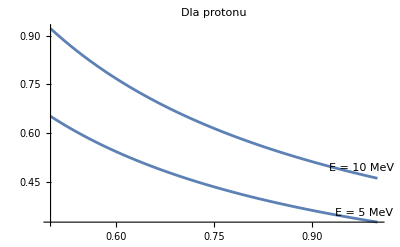

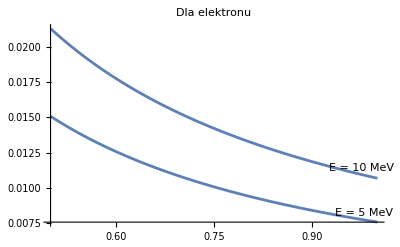

```mathematica
Show[Plot[Values[odleg   /.vc -> Values[oblV]/. Ec-> 5 *10^6*e /. m->mp],{B,0.5,1.0}, PlotLabel->"Dla protonu, Energia = 5 MeV", DisplayFunction->Identity, PlotLabels->Placed["E = 5 MeV",Bottom]],
Plot[Values[odleg   /.vc -> Values[oblV]/. Ec-> 10 *10^6*e /. m->mp],{B,0.5,1.0}, PlotLabel->"Dla protonu, Energia = 10 MeV", DisplayFunction->Identity, PlotLabels->Placed["E = 10 MeV",Bottom]],PlotRange->All, PlotLabel->"Dla protonu"]
Show[Plot[Values[odleg   /.vc -> Values[oblV]/. Ec-> 5 *10^6*e /. m->me],{B,0.5,1.0}, PlotLabel->"Dla elektronu, Energia = 5 MeV", DisplayFunction->Identity, PlotLabels->Placed["E = 5 MeV",Bottom]],
Plot[Values[odleg   /.vc -> Values[oblV]/. Ec-> 10 *10^6*e /. m->me],{B,0.5,1.0}, PlotLabel->"Dla elektronu, Energia = 10 MeV", DisplayFunction->Identity, PlotLabels->Placed["E = 10 MeV",Bottom]],{PlotRange->All}, PlotLabel->"Dla elektronu"]
```